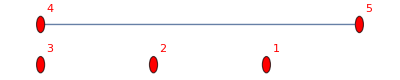
{{},{-Graphics-},{-Graphics-},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Table[
Map[Graph[VertexList[#],EdgeList[GraphComplement[#]],GraphLayout->"TutteEmbedding",VertexStyle->Red,VertexLabels->"Name"]&,Select[BarelyNColorableGraphsOfCount[count],PlanarGraphQ]],
{count,3,20}]
```

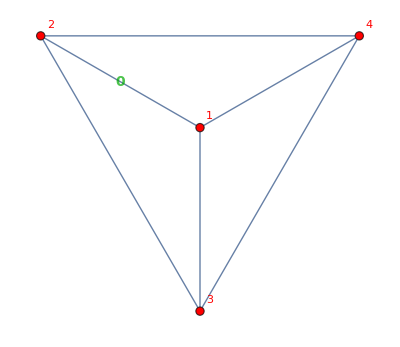
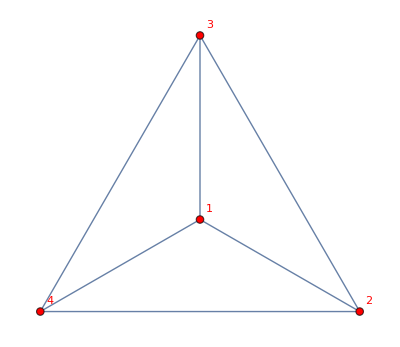
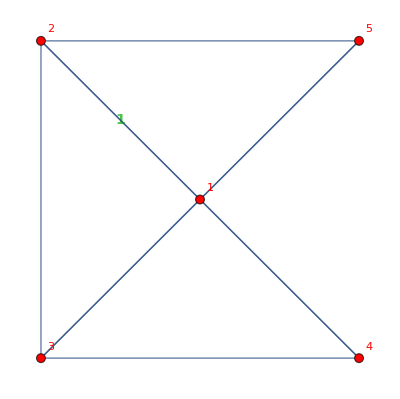
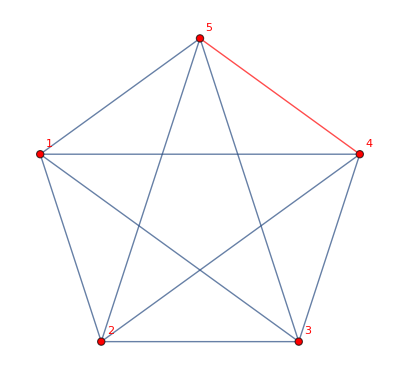
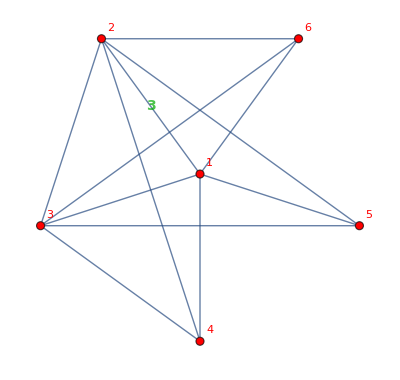
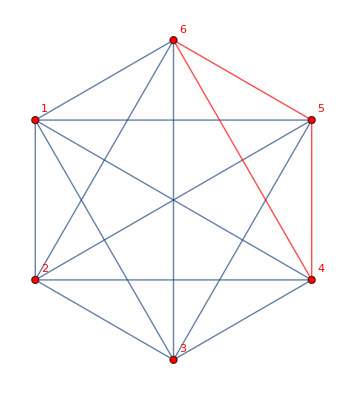
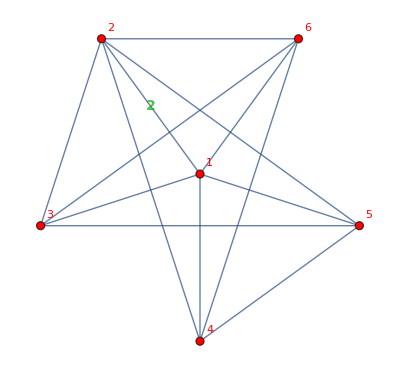
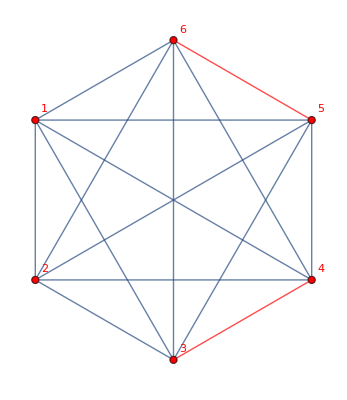
3→{}
4→{{-Graphics-,-Graphics-}}
5→{{-Graphics-,-Graphics-}}
6→{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}
7→{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[
count->Map[{#,CompleteGraph[VertexCount[#],EdgeStyle->Table[k->{Red,Thick},{k,EdgeList[GraphComplement[#]]}],VertexStyle->Red,VertexLabels->"Name"]}&,BarelyNColorableGraphsOfCount[count]],
{count,3,7}]//TableForm
```

```mathematica
Select[BarelyNColorableGraphsOfCount[8],PlanarGraphQ]
```

{}

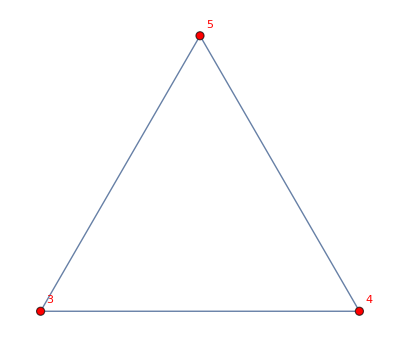
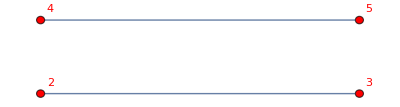

```mathematica
Map[Graph[EdgeList[GraphComplement[#]],GraphLayout->"TutteEmbedding",VertexStyle->Red,VertexLabels->"Name"]&,Select[BarelyNColorableGraphsOfCount[5,3],PlanarGraphQ]]
```

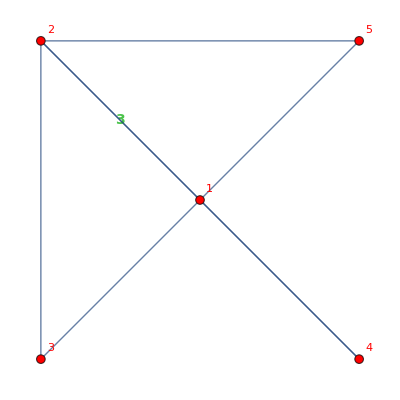
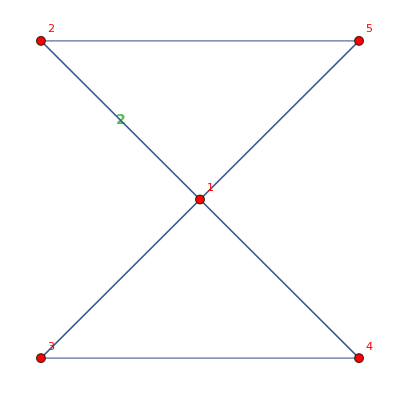

```mathematica
BarelyNColorableGraphsOfCount[5,3]
```

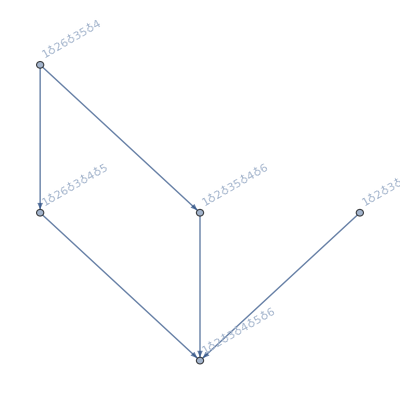

```mathematica
Graph[{1<->2,1<->3,3<->2,1<->4,4<->2,4<->3,1<->5,2<->5,4<->5,1<->6,3<->6,4<->6},GraphLayout->"TutteEmbedding"]//FindFullFormula//FormulaGraphReverse
```

```mathematica
Table[Sort[Tally[With[{g=Graph[plantri[[k]]]},Table[VertexDegree[g,v],{v,VertexList[g]}]]]],{k,1,10}]
```

{{{5,12}},{{5,12},{6,2}},{{5,12},{6,3}},{{5,12},{6,4}},{{5,12},{6,4}},{{5,14},{7,2}},{{5,12},{6,5}},{{5,12},{6,5}},{{5,13},{6,3},{7,1}},{{5,12},{6,5}}}

```mathematica
Table[With[{g=Graph[plantri[[k]]]},MaximalPlanarQ[g]],{k,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
FilterFormula[form_,vertices_]:=Block[{setList=Map[SymbolToSets,form],sets2},
sets2=Map[Map[Select[#,MemberQ[vertices,#]&]&,#]&,setList];
sets2=Table[Select[f,#≠{}&],{f,sets2}];
sets2=Table[Sort[Map[Sort,f]],{f,sets2}];
Sort[Tally[Map[SetsToSymbol[#]&,sets2]]]
]
```

```mathematica
FilterFormula[{v2cx36ax48bx579,v2ax36cx48bx579,v29bx37ax468x5c,v29bx37ax46cx58,v29bx357x4cx68a,v29bx35cx47x68a,v29bx357x46cx8a,v29bx35cx468x7a,v259x37ax48bx6c,v25cx37ax48bx69,v25cx37ax468x9b,v259x37ax46cx8b,v259x36cx48bx7a,v25cx36ax48bx79,v24bx3cx579x68a,v24cx3bx579x68a,v24cx36ax579x8b,v24bx36cx579x8a,v24cx357x68ax9b,v24bx35cx68ax79},{2,3,4,5,6}]
```

{{2♁35♁46,2},{24♁35♁6,2},{24♁36♁5,2},{25♁3♁46,2},{25♁36♁4,2},{2♁3♁46♁5,2},{2♁35♁4♁6,2},{2♁36♁4♁5,2},{24♁3♁5♁6,2},{25♁3♁4♁6,2}}

```mathematica
FilterFormula2[{v2cx36ax48bx579,v2ax36cx48bx579,v29bx37ax468x5c,v29bx37ax46cx58,v29bx357x4cx68a,v29bx35cx47x68a,v29bx357x46cx8a,v29bx35cx468x7a,v259x37ax48bx6c,v25cx37ax48bx69,v25cx37ax468x9b,v259x37ax46cx8b,v259x36cx48bx7a,v25cx36ax48bx79,v24bx3cx579x68a,v24cx3bx579x68a,v24cx36ax579x8b,v24bx36cx579x8a,v24cx357x68ax9b,v24bx35cx68ax79},{2,3,4,5,6}]
```

{{3,10},{4,10}}

```mathematica
FindFullFormula4[CycleGraph[5]]
```

{v1x2x35x4,v1x25x3x4,v1x24x3x5,v14x2x3x5,v13x2x4x5}

```mathematica
PrintAssoc[assoc_]:=Table[{k,Framed[Column[assoc[k]]]},{k,Keys[assoc]}]
```

```mathematica
PrintFormula[form_]:=Block[{assoc=GroupBy[form,SymbolLevel[#[[1]]]&]
},Table[{Style[ToString[k]<>" → ",Red,14],Framed[Column[Map[{SymbolToLabel[#[[1]]],#[[2]]}&,assoc[k]]],FrameStyle->If[Length[assoc[k]]==5,Black,Red]],Style[Total[Map[#[[2]]&,assoc[k]]],Blue,14]},{k,Keys[assoc]}]
]
```

```mathematica
SymbolToSets[v19x35xa]//SetsToSymbol
```

v19x35xa

```mathematica
FilterFormula2[form_,vertices_]:=Block[{setList=Map[SymbolToSets,form],sets2},
sets2=Map[Map[Select[#,MemberQ[vertices,#]&]&,#]&,setList];
sets2=Table[Select[f,#≠{}&],{f,sets2}];
sets2=Table[Sort[Map[Sort,f]],{f,sets2}];
Map[{#[[1]],Style[#[[2]],If[#[[2]]==5,Black,Red]]}&,Sort[Tally[Map[SymbolLevel,DeleteDuplicates[Map[SetsToSymbol[#]&,sets2]]]]]]
]
```

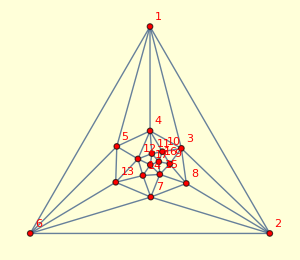
{-Graphics-→1<->3 | 5
4 | 5
2<->3 | 5
4 | 5
5<->3 | 5
4 | 5
6<->3 | 5
4 | 5
8<->3 | 4
4 | 5
9<->3 | 5
4 | 5
10<->3 | 5
4 | 5
11<->3 | 5
4 | 5
13<->3 | 5
4 | 5
14<->3 | 4
4 | 5
16<->3 | 5
4 | 5
17<->3 | 5
4 | 5}

```mathematica
Table[With[{g=Graph[plantri[[k]]]},Framed[Graph[g,VertexStyle->Red,VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->300,Background->LightYellow]]->
TableForm[Table[
With[{h=Graph[VertexDelete[g,v],VertexStyle->Red,VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->200],neigh=VertexList[VertexDelete[NeighborhoodGraph[g,v],v]]},
{v<->TableForm[FilterFormula2[FindFullFormula4[h],neigh],TableDepth->2]}
],{v,Sort[Select[VertexList[g],VertexDegree[g,#]==5&]]}]]
],{k,{8}}]
```

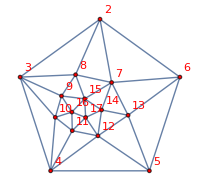
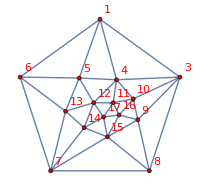
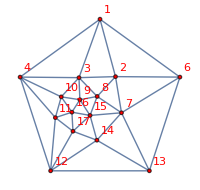
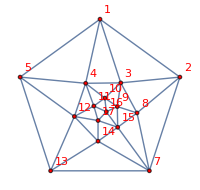
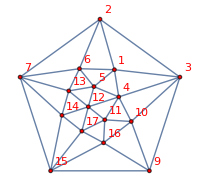
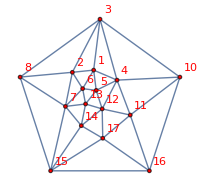
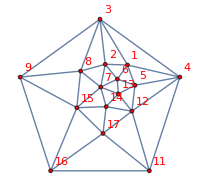
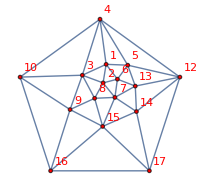
{-Graphics-→{{-Graphics-1<->3 →  | {2♁35♁46,6}
{3♁25♁46,5}
{4♁25♁36,2}
{5♁24♁36,3}
{6♁24♁35,6} | 22
4 →  | {2♁3♁5♁46,10}
{2♁4♁5♁36,7}
{2♁4♁6♁35,10}
{3♁4♁6♁25,9}
{3♁5♁6♁24,10} | 46},{-Graphics-2<->3 →  | {1♁37♁68,7}
{3♁17♁68,6}
{6♁18♁37,4}
{7♁18♁36,2}
{8♁17♁36,3} | 22
4 →  | {1♁3♁7♁68,10}
{1♁6♁8♁37,9}
{1♁7♁8♁36,7}
{3♁6♁7♁18,7}
{3♁6♁8♁17,8} | 41},{-Graphics-5<->3 →  | {1♁4d♁6c,3}
{4♁1d♁6c,2}
{6♁1c♁4d,6}
{c♁1d♁46,5}
{d♁1c♁46,6} | 22
4 →  | {1♁4♁d♁6c,7}
{1♁6♁c♁4d,10}
{1♁c♁d♁46,10}
{4♁6♁c♁1d,9}
{4♁6♁d♁1c,10} | 46},{-Graphics-6<->3 →  | {1♁2d♁57,6}
{2♁1d♁57,3}
{5♁17♁2d,6}
{7♁1d♁25,4}
{d♁17♁25,3} | 22
4 →  | {1♁2♁d♁57,8}
{1♁5♁7♁2d,12}
{1♁7♁d♁25,9}
{2♁5♁7♁1d,9}
{2♁5♁d♁17,8} | 46},{-Graphics-8<->3 →  | {2♁3f♁79,3}
{7♁29♁3f,8}
{9♁2f♁37,3}
{f♁29♁37,8} | 22
4 →  | {2♁3♁f♁79,6}
{2♁7♁9♁3f,9}
{2♁9♁f♁37,9}
{3♁7♁9♁2f,6}
{3♁7♁f♁29,11} | 41},{-Graphics-9<->3 →  | {3♁8g♁af,6}
{8♁3g♁af,3}
{a♁3f♁8g,7}
{f♁3g♁8a,2}
{g♁3f♁8a,4} | 22
4 →  | {3♁8♁g♁af,8}
{3♁a♁f♁8g,10}
{3♁f♁g♁8a,7}
{8♁a♁f♁3g,7}
{8♁a♁g♁3f,9} | 41},{-Graphics-10<->3 →  | {3♁4g♁9b,5}
{4♁3g♁9b,2}
{9♁3b♁4g,6}
{b♁3g♁49,3}
{g♁3b♁49,6} | 22
4 →  | {3♁4♁g♁9b,9}
{3♁9♁b♁4g,10}
{3♁b♁g♁49,10}
{4♁9♁b♁3g,7}
{4♁9♁g♁3b,10} | 46},{-Graphics-11<->3 →  | {4♁ah♁cg,2}
{a♁4h♁cg,3}
{c♁4g♁ah,5}
{g♁4h♁ac,6}
{h♁4g♁ac,6} | 22
4 →  | {4♁a♁h♁cg,7}
{4♁c♁g♁ah,9}
{4♁g♁h♁ac,10}
{a♁c♁g♁4h,10}
{a♁c♁h♁4g,10} | 46},{-Graphics-13<->3 →  | {5♁6e♁7c,7}
{6♁5e♁7c,4}
{7♁5e♁6c,2}
{c♁57♁6e,6}
{e♁57♁6c,3} | 22
4 →  | {5♁6♁e♁7c,9}
{5♁7♁c♁6e,10}
{5♁7♁e♁6c,7}
{6♁7♁c♁5e,7}
{6♁c♁e♁57,8} | 41},{-Graphics-14<->3 →  | {7♁cf♁dh,8}
{d♁7h♁cf,3}
{f♁7c♁dh,8}
{h♁7c♁df,3} | 22
4 →  | {7♁c♁f♁dh,11}
{7♁c♁h♁df,6}
{7♁d♁h♁cf,9}
{c♁d♁f♁7h,6}
{d♁f♁h♁7c,9} | 41},{-Graphics-16<->3 →  | {9♁ah♁bf,3}
{a♁9h♁bf,6}
{b♁9h♁af,6}
{f♁9b♁ah,4}
{h♁9b♁af,3} | 22
4 →  | {9♁a♁h♁bf,8}
{9♁b♁f♁ah,9}
{9♁b♁h♁af,8}
{a♁b♁f♁9h,12}
{a♁f♁h♁9b,9} | 46},{-Graphics-17<->3 →  | {b♁cf♁eg,7}
{c♁bf♁eg,6}
{e♁bf♁cg,3}
{f♁be♁cg,2}
{g♁be♁cf,4} | 22
4 →  | {b♁c♁f♁eg,10}
{b♁e♁f♁cg,7}
{b♁e♁g♁cf,9}
{c♁e♁g♁bf,8}
{c♁f♁g♁be,7} | 41}}}

```mathematica
Table[With[{g=Graph[plantri[[k]]]},Framed[Graph[g,VertexStyle->Red,VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->300,Background->LightYellow]]->
Table[
With[{h=Graph[VertexDelete[g,v],VertexStyle->Red,VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->200],neigh=VertexList[VertexDelete[NeighborhoodGraph[g,v],v]]},
{Labeled[h,Style[v,Darker[Green],12]]<->TableForm[PrintFormula[FilterFormula[FindFullFormula4[h],neigh]],TableDepth->2]}
],{v,Sort[Select[VertexList[g],VertexDegree[g,#]==5&]]}]
],{k,{8}}]
```